Global Variables

```mathematica
prec=100;

Nmax = 100;

x1 = 1.0;
x2 = 10.0;
x3 = 20.0;

xmax = 20.0;
xmin = -20.0;
xsize = 100;
dx=(xmax-xmin)/(xsize-1);

Xvector = N[Range[xmin,xmax,dx],prec];
Nvector = Range[0,Nmax,1];
```

Wavefuntion_Wolfram_Mathematica_1

```mathematica
WavefunctionMathematica1[n_,x_,prec_]:=Module[{nPrec,xPrec,norm,H,wavefunction},
SetPrecision[n,prec];
SetPrecision[x,prec];
norm=(2^(-0.5*n))*(Gamma[n+1]^(-0.5))*(Pi^(-0.25));
H=HermiteH[n,x];
wavefunction=SetPrecision[norm*Exp[-0.5*x^2]*H,prec];
wavefunction];
```

Wavefuntion_Wolfram_Mathematica_2

```mathematica
WavefunctionMathematica2[n_,x_,prec_]:=Module[{wavefunction,xsize,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
wavefunction[[2]]=SetPrecision[(2 x wavefunction[[1]])/Sqrt[2],prec];
For[i=3,i<=n+1,i++,wavefunction[[i]]=2 x (wavefunction[[i-1]]/Sqrt[2 (i-1)])-Sqrt[(i-2)/(i-1)] wavefunction[[i-2]];];
wavefunction[[n+1]]];
```

Wavefuntion_Wolfram_Mathematica_3

```mathematica
WavefunctionMathematica3[n_,x_,prec_]:=Module[{wavefunction,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
For[i=1,i<=n,i++,
wavefunction[[i+1]]=
SetPrecision[2 x (wavefunction[[i]]/Sqrt[2 (i)])-
Sqrt[(i-1)/i] wavefunction[[i-1]],prec]];

wavefunction];
```

#### Tests

Single-Mode and Onedimensional Function with x = 1.0

Functionality Test Passed: True

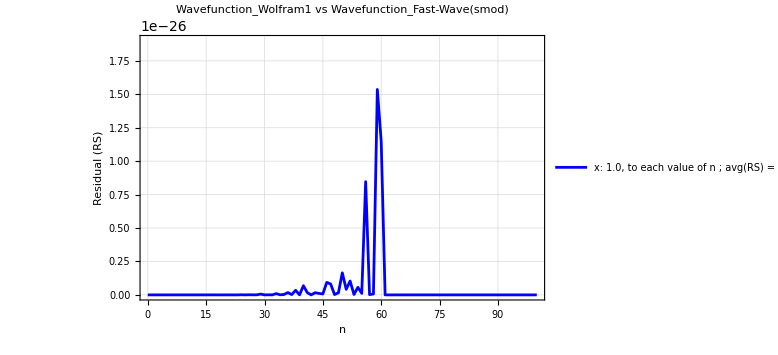

```mathematica
FastWaveSMOdN100x1=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import numpy as np;N_max = 100;x1 = 1.0;np.array([wavefunction_smod(n,x1) for n in range(N_max+1)]);"]],prec];

(*WolframSMOdN100x1 = WavefunctionMathematica3[Nmax,x1,prec];*)
WolframSMOdN100x1 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMOdN100x1,WavefunctionMathematica1[i-1,x1,prec]];]

Residual = (WolframSMOdN100x1-FastWaveSMOdN100x1)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{"x: 1.0, to each value of n ; \n avg(RS) = " <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]},Below],
ImageSize->Large,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-25.8)}}
 ]
```

#### Single-Mode and Onedimensional Less Fast Function with x = 1.0

Functionality Test Passed: True

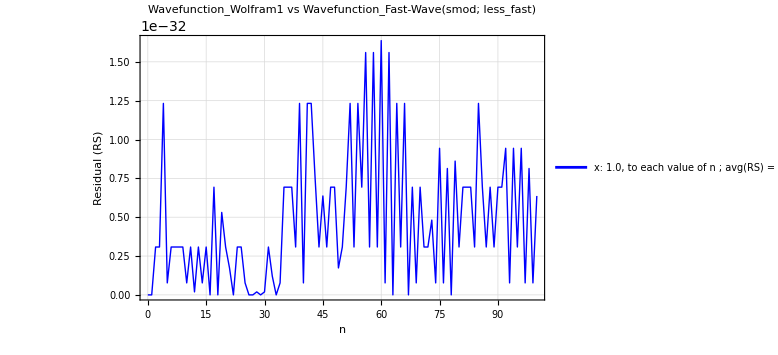

```mathematica
FastWaveSMOdN100x1=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import numpy as np;N_max = 100;x1 = 1.0;np.array([wavefunction_smod(n,x1,more_fast=False) for n in range(N_max+1)]);"]],prec];

(*WolframSMOdN100x1 = WavefunctionMathematica3[Nmax,x1,prec];*)
WolframSMOdN100x1 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMOdN100x1,WavefunctionMathematica1[i-1,x1,prec]];]

Residual = (WolframSMOdN100x1-FastWaveSMOdN100x1)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod; less_fast)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{"x: 1.0, to each value of n ; \n avg(RS) = " <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]},Below],
ImageSize->Large
 ]
```

#### Single-Mode and Onedimensional Function with x = 10.0

Functionality Test Passed: True

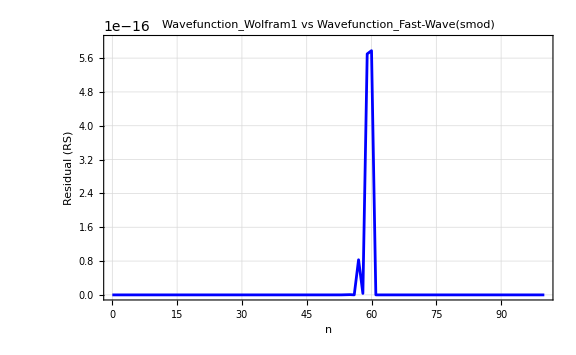

```mathematica
FastWaveSMOdN100x2=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import numpy as np;N_max = 100;x2 = 10.0;np.array([wavefunction_smod(n,x2) for n in range(N_max+1)]);"]],prec];

(*WolframSMOdN100x2 = WavefunctionMathematica3[Nmax,x2,prec];*)

WolframSMOdN100x2 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMOdN100x2,WavefunctionMathematica1[i-1,x2,prec]];]

Residual = (WolframSMOdN100x2-FastWaveSMOdN100x2)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 10.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-15.3)}}
]
```

#### Single-Mode and Onedimensional Less Fast Function with x = 10.0

Functionality Test Passed: True

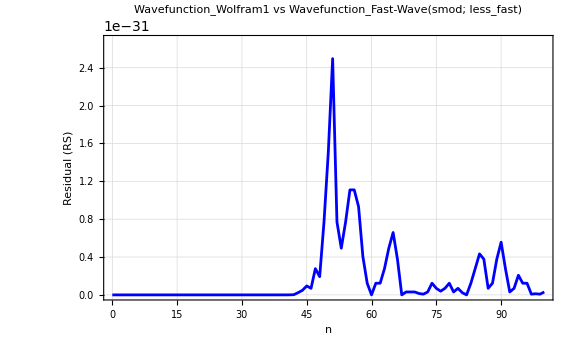

```mathematica
FastWaveSMOdN100x2=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import numpy as np;N_max = 100;x2 = 10.0;np.array([wavefunction_smod(n,x2,more_fast=False) for n in range(N_max+1)]);"]],prec];

(*WolframSMOdN100x2 = WavefunctionMathematica3[Nmax,x2,prec];*)

WolframSMOdN100x2 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMOdN100x2,WavefunctionMathematica1[i-1,x2,prec]];]

Residual = (WolframSMOdN100x2-FastWaveSMOdN100x2)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod; less_fast)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 10.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-30.65)}}
]
```

#### Single-Mode and Onedimensional Function with x = 20.0

Functionality Test Passed: True

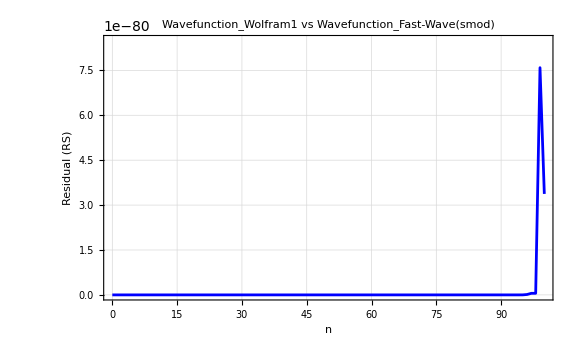

```mathematica
FastWaveSMOdN100x3=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import numpy as np;N_max = 100;x3 = 20.0;np.array([wavefunction_smod(n,x3) for n in range(N_max+1)]);"]],prec];

(*WolframSMOdN100x3 = WavefunctionMathematica3[Nmax,x3,prec];*)
WolframSMOdN100x3 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMOdN100x3,WavefunctionMathematica1[i-1,x3,prec]];]

Residual =( WolframSMOdN100x3-FastWaveSMOdN100x3)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 20.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-79.15)}}
]
```

#### Single-Mode and Onedimensional Less Fast Function with x = 20.0

Functionality Test Passed: True

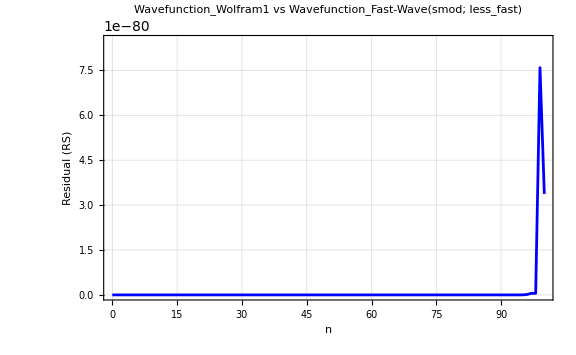

```mathematica
FastWaveSMOdN100x3=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import numpy as np;N_max = 100;x3 = 20.0;np.array([wavefunction_smod(n,x3, more_fast= False) for n in range(N_max+1)]);"]],prec];

(*WolframSMOdN100x3 = WavefunctionMathematica3[Nmax,x3,prec];*)
WolframSMOdN100x3 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMOdN100x3,WavefunctionMathematica1[i-1,x3,prec]];]

Residual =( WolframSMOdN100x3-FastWaveSMOdN100x3)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod; less_fast)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 20.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-79.15)}}
]
```

#### Single-Mode and Multidimensional Function with X = [(-20) → 20; 100]

Functionality Test Passed: True

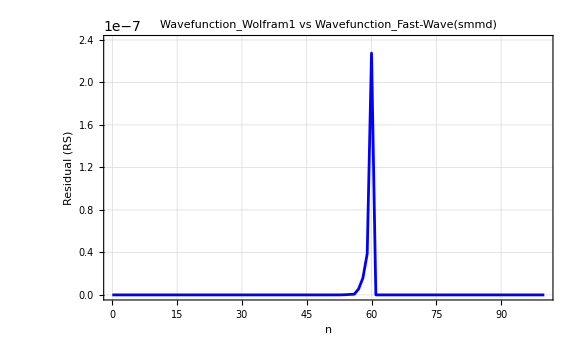

```mathematica
FastWaveSMMdN100X=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smmd;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);np.array([wavefunction_smmd(n,X) for n in range(N_max+1)]);"]],prec];

(*WolframSMMdN100X = WavefunctionMathematica3[Nmax,Xvector,prec];*)
WolframSMMdN100X = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMMdN100X,WavefunctionMathematica1[i-1,Xvector,prec]];]


ResidualMatrix =(WolframSMMdN100X - FastWaveSMMdN100X)^2;

Residual = Mean /@ResidualMatrix;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smmd)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" X: [(-20)→20;100], to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-6.7)}}
 ]
```

#### Single-Mode and Multidimensional Less Fast Function with X = [(-20) → 20; 100]

Functionality Test Passed: True

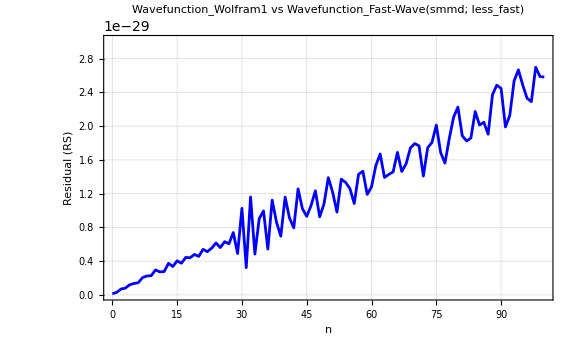

```mathematica
FastWaveSMMdN100X=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smmd;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);np.array([wavefunction_smmd(n,X,more_fast=False) for n in range(N_max+1)]);"]],prec];

(*WolframSMMdN100X = WavefunctionMathematica3[Nmax,Xvector,prec];*)
WolframSMMdN100X = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMMdN100X,WavefunctionMathematica1[i-1,Xvector,prec]];]


ResidualMatrix =(WolframSMMdN100X - FastWaveSMMdN100X)^2;

Residual = Mean /@ResidualMatrix;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smmd; less_fast)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" X: [(-20)→20;100], to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-28.6)}}
 ]
```

#### Multi-Mode and Onedimensional Function with x = 1.0

Functionality Test Passed: True

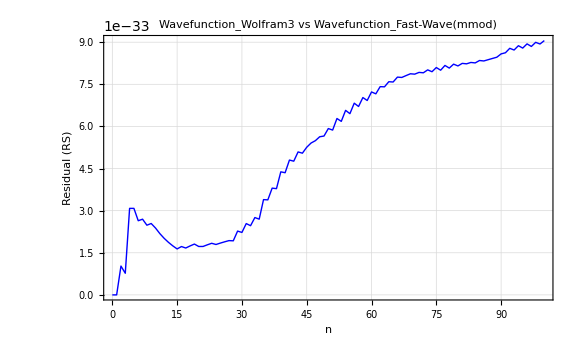

```mathematica
FastWaveMMOdN100x1=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_mmod;import numpy as np;N_max = 100;x1 =1.0;[wavefunction_mmod(n,x1) for n in range(N_max+1)];"]],prec];

WavefunctionMMOdN100x1 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionMMOdN100x1 ,WavefunctionMathematica3[i-1,x1,prec]];]
ResidualList = (WavefunctionMMOdN100x1 - FastWaveMMOdN100x1)^2;

Residual = Mean /@ResidualList;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mmod)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 1.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```

#### Multi-Mode and Onedimensional Function with x = 10.0

Functionality Test Passed: True

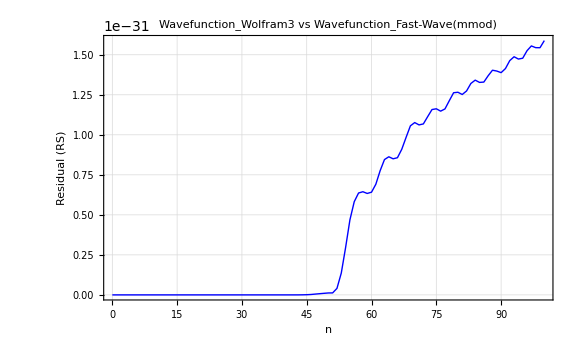

```mathematica
FastWaveMMOdN100x10=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_mmod;import numpy as np;N_max = 100;x2 =10.0;[wavefunction_mmod(n,x2) for n in range(N_max+1)];"]],prec];

WavefunctionMMOdN100x10 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionMMOdN100x10 ,WavefunctionMathematica3[i-1,x2,prec]];]
ResidualList = (WavefunctionMMOdN100x10 - FastWaveMMOdN100x10)^2;

Residual = Mean /@ResidualList;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mmod)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 10.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```

#### Multi-Mode and Onedimensional Function with x = 20.0

Functionality Test Passed: True

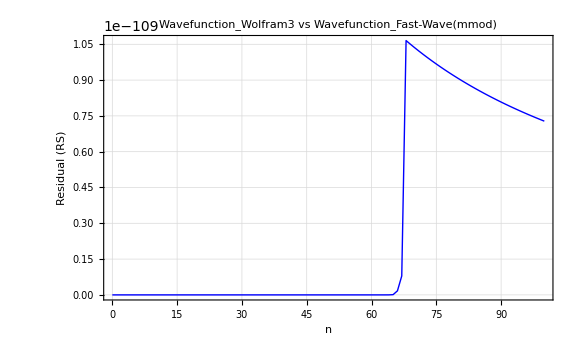

```mathematica
FastWaveMMOdN100x20=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_mmod;import numpy as np;N_max = 100;x3 =20.0;[wavefunction_mmod(n,x3) for n in range(N_max+1)];"]],prec];

WavefunctionMMOdN100x20 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionMMOdN100x20 ,WavefunctionMathematica3[i-1,x3,prec]];]
ResidualList = (WavefunctionMMOdN100x20 - FastWaveMMOdN100x20)^2;

Residual = Mean /@ResidualList;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mmod)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 20.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```

#### Multi-Mode and Multidimensional Function with X = [(-20) → 20; 100]

Functionality Test Passed: True

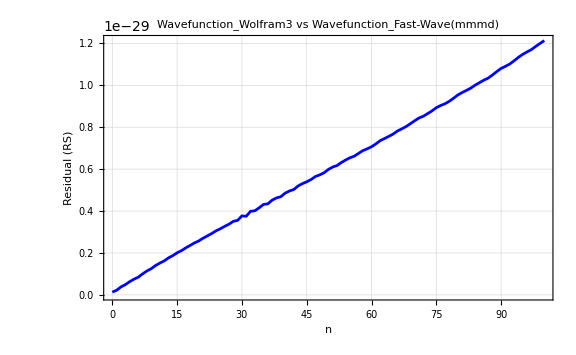

```mathematica
FastWaveMMMdN100X=SetPrecision[Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_mmmd;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[wavefunction_mmmd(n,X) for n in range(N_max+1)];"]],prec];

WolframSMMdN100X = {};

For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSMMdN100X,WavefunctionMathematica3[i-1,Xvector,prec]];]

ResidualMatrixList = (WolframSMMdN100X - FastWaveMMMdN100X)^2;

Residual = Mean/@(Flatten/@ResidualMatrixList);

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mmmd)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" X: [(-20)→20;100], to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```